# Sucesiones.

1. Calcula el límite de la sucesión     ((2n+1)/(2n-√n))^(√(n+2)) cuando  n tiende a infinito.

```mathematica
Limit[((2n+1)/(2n-√n))^(√(n+2)),n-> Infinity]
```

√ⅇ

2 .	Calcula los límites que consideres oportuno para comparar el orden de magnitud de las siguientes suceciones:  a_n=√(n^5)-√(n^3+1) y  b_n=log(n)

```mathematica
Limit[(√(n^5)-√(n^3+1))/(Log[n]),n-> Infinity]
```

∞

El límite del cociente    Limit [a_n/b_n ,n→ Infinity]=     ∞
         Por lo tanto podemos concluir que     √(n^5)-√(n^3+1))>>(Log[n]

3.  Resuelve la recurrencia:
                               a_1    = 1
                               a_(n+1) =a_n  √5 n≥1
y encuentra   a_15

```mathematica
RSolve[{a[n+1]==a[n]  √5, a[1]==1},a[n],n]
```

{{a[n]→5^(-1/2+n/2)}}

```mathematica
%/.n->15
```

{{a[15]→78125}}

a_n=     5^(-1/2+n/2)               
           a_15=78125

4. 	Obtén los 10 primeros términos de la sucesión anterior y represéntalos graficamente.

```mathematica
List1=Table[5^(-1/2+n/2)     ,{n,1,10}]
```

{1,√5,5,5 √5,25,25 √5,125,125 √5,625,625 √5}

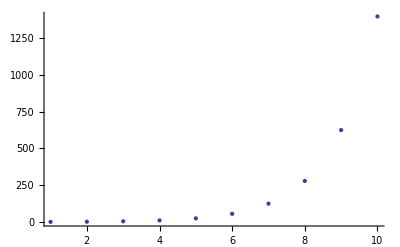

```mathematica
ListPlot[List1]
```